# Report: Project 1

Course code: II1303
Date: 2022-11-28

Anton Herdin Ringstedt, antonhr@kth.se
Hein Lee, hein@kth.se
Muttakin Karim, muttakin@kth.se

# Part 1:

## Summary

### Task

a)  	1. Write received signal r(t) in the form A(d)cos(2πfc + ϕ(d)).
	    And express the power of the received signal as a function of d.
	2.  Plot the power between d = 0, to d = 2 km. One in linear scale, and one in dB.

b)	      Repeat step two, but account for propagation loss in the power function.

### Result

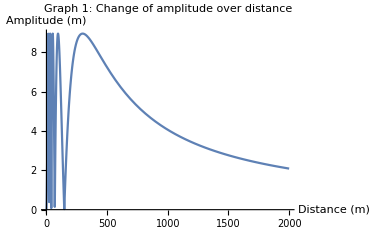

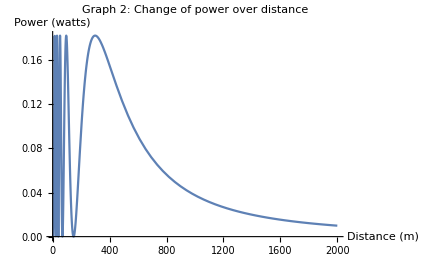
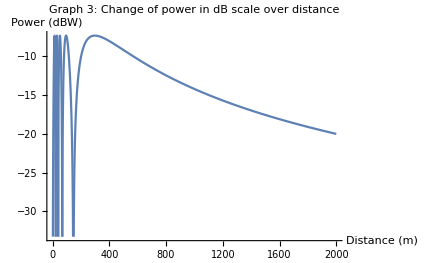

-Graphics- -Graphics-

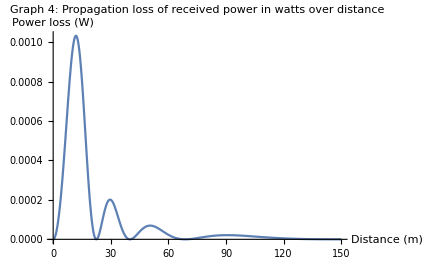
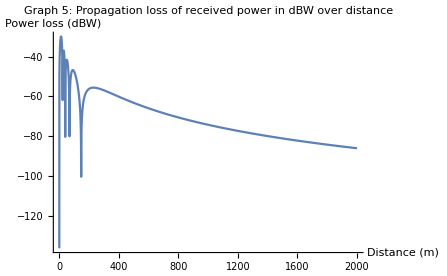

## Explaining the methods

First, the figure in the question was broken down into a simple diagram as shown below. The radio tower is represented by the dot on the top left and the mobile radio unit is shown by the dot in the middle right. The reflected and direct signals are demonstrated by the arrows. The extension of the reflected signal was then used to form a triangle. The hypotenuse of this triangle was used to calculate the direct path of the wave.  
-Graphics-

The frequency of the received signal, r(t)=s(t-τ1)-s(t-τ2), was used alongside equation: s(t)=√Pcos(2fc t)to calculate the real and imaginary parts of the reflected wave. The details of the calculations are shown in the Code section. The amplitude and the phase shift of the wave was calculated using trigonometry and this was then used to plot the graph showing how the amplitude varied over a distance of 0 to 2km. 

Additionally, the wavelength was then figured out by the frequency and the speed of the wave. The equations of power and propagation due to power loss was used to plot graphs.

## Discussing the results

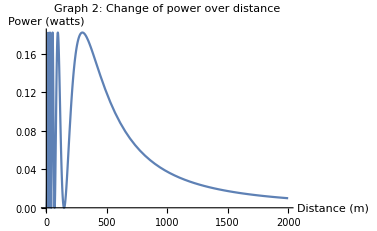
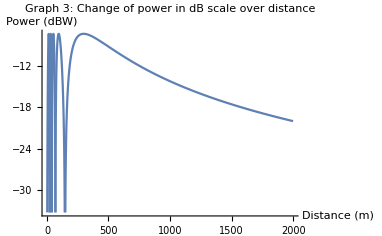
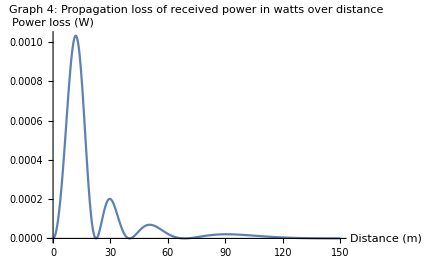
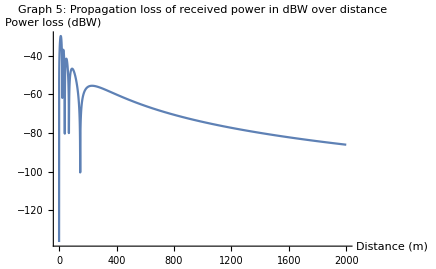
-Graphics-
The first graph shows how the amplitude of the sinus wave varies over a distance of 0 to 2km. From the graph it is noted that around 300m the amplitude of the wave begins to drop and goes towards zero. This is called the turning point of the curve and from the equation used it can be seen that during this point the real and imaginary parts cancel out themselves. The distance d in the real and imaginary parts eventually grow to such proportions that any other constants in the equation becomes irrelevant, and the two Cos and Sin cancel themselves out.  


-Graphics-                                                -Graphics-

Graphs 2 and 3 show how the change of power received over distance. From the two graphs it seems that power reduces when distance is increased. Form graph 2 it is seen that the power oscillates up to a distance of 300 meters and then starts dropping. By looking at the given equation, it is deemed that this is a result of the change of amplitude, power is proportional to the power of the amplitude. So as the amplitude drops the power also drops. The decibel watts demonstration in graph 3 follows a logarithmic scale. This makes it easier to draw comparisons, as the values of power can now be compared to a fixed constant, 1W. 


-Graphics--Graphics-

Graphs 4 and 5 demonstrates the decaying of propagation power loss. From graph 4 it seen that the power received decreases exponentially as the distance increases. This is because power loss is inversely proportional to the square of the distance. As a result as the distance is doubled the power is reduced quadratically. This means that as distance increases the signal strength is reduced drastically. The logarithmic scale in graph 5 helps to compare the power loss and this helps to draw suitable conclusions.

## Code section

```mathematica
P=20; (*dBW, 100 watts*)
```

```mathematica
Fc=500 *10^6; (*MHz*)
```

```mathematica
s[t_]:=√P Cos[2 π Fc t ]
```

```mathematica
c=3*10^8; (*speed of light*)
```

```mathematica
(*Figure of radio tower and mobile radio unit.*)
(*Shows direct signal, and reflected signal*)
(*The reflected signal can be extended down into a triangle to obtain the hypotenuse*)
```

```mathematica
-Graphics-
(*Dividing the hypotenuse by c, the time delay is obtained*)
```

-Graphics-

```mathematica
τ1=(√(d^2+28.5^2))/c;(*time delay, direct path*)
```

```mathematica
τ2=(√(d^2+31.5^2))/c;(*time delay, reflected path*)
```

```mathematica
r[t_]:=s[(t-τ1)]-s[(t-τ2)] (*recived signal*)
```

```mathematica
r[t]
```

2 √5 Cos[1000000000 π (-(√(812.25+d^2))/300000000+t)]-2 √5 Cos[1000000000 π (-(√(992.25+d^2))/300000000+t)]

```mathematica
(*phasor in polar form*)
```

```mathematica
Polar1=2 √5 (Cos[2π Fc  (-(√(812.25+d^2))/c)]-ⅈ Sin[2π Fc  (-(√(812.25+d^2))/c)]); (*phasor in polar form*)
```

```mathematica
Polar2=2 √5 (Cos[2π Fc  (-(√(992.25+d^2))/c)]-ⅈ Sin[2π Fc  (-(√(992.25+d^2))/c)]);
```

```mathematica
(*real phasor addition*)
```

```mathematica
real=2 √5(Cos[2π Fc (-(√(812.25+d^2))/c)]- Cos[2π Fc  (-(√(992.25+d^2))/c)]);
```

```mathematica
(*imaginary phasor addition*)
```

```mathematica
im=2 √5(-Sin[2π Fc (-(√(812.25+d^2))/c)]+Sin[2π Fc  (-(√(992.25+d^2))/c)]);
```

```mathematica
Amp=√(real^2+im^2); (*amplitude, A(d)*)
Phi=ArcTan[im/real]; (*phase, phi(d)*)
```

```mathematica
Rpow[t_]:=Amp Cos[2π Fc t + Phi]; (*Signal r(d) in A(d)Cos(2π Fc t + Phi(d)) form*)
```

```mathematica
Rpow[t]
```

Cos[1000000000 π t+ArcTan[(Sin[10/3 √(812.25+d^2) π]-Sin[10/3 √(992.25+d^2) π])/(Cos[10/3 √(812.25+d^2) π]-Cos[10/3 √(992.25+d^2) π])]] √(20 (Cos[10/3 √(812.25+d^2) π]-Cos[10/3 √(992.25+d^2) π])^2+20 (Sin[10/3 √(812.25+d^2) π]-Sin[10/3 √(992.25+d^2) π])^2)

```mathematica
(*plot of amplitude*)
```

```mathematica
Plot[Amp,{d,0,2000},AxesLabel->{"Distance (m)","Amplitude (m)"}, PlotLabel->"Graph 1: Change of amplitude over distance"]
```

-Graphics-

```mathematica
λ=c/Fc; (*radio-wavelength*)
```

```mathematica
power=λ^2/(4π)^2 Amp^2; (*power of recived signal*)
```

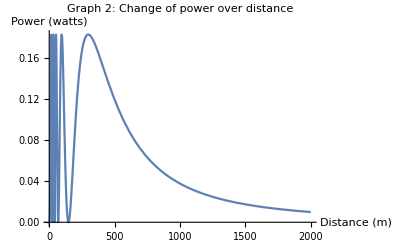

```mathematica
Plot[power,{d,0,2000},AxesLabel->{"Distance (m)","Power (watts)"}, PlotLabel->"Graph 2: Change of power over distance"] (*power, linear*)
```

```mathematica
DB=10Log10[power];
```

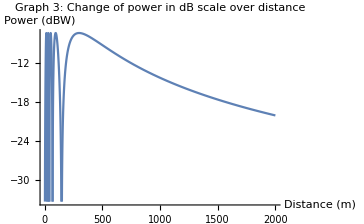

```mathematica
Plot[DB,{d,0,2000},AxesLabel->{"Distance (m)","Power (dBW)"}, PlotLabel->"Graph 3: Change of power in dB scale over distance"] (*power, dB scale*)
```

```mathematica
(*Del b) med decay*)
```

```mathematica
powerdecay=λ^2/((4π)^2*d^2)Amp^2; (*power*)
```

```mathematica
Plot[powerdecay,{d,0,150},PlotRange -> Full, AxesLabel->{"Distance (m)","Power loss (W)"}, PlotLabel->"Graph 4: Propagation loss of received power in watts over distance"] (*power, with decay*)
```

-Graphics-

```mathematica
DBdecay=10Log10[powerdecay];
```

```mathematica
Plot[DBdecay,{d,0,2000}, AxesLabel->{"Distance (m)","Power loss (dBW)"}, PlotLabel->"Graph 5: Propagation loss of received power in dBW over distance"] (*power, dB scale with decay*)
```

-Graphics-

# Part 2:

## Summary

### Task

a)  	Find Period and Fourier Series Representation of signal

b)	Synthesis signal with Fourier Synthesis Summation.

c) 	Find N so signal will be free of Aliasing. Assume Fs = 8000 Hz

d)	Find N so signal will be free of Aliasing. Assume Fs = 1000 Hz

e)	Draw the synthesized spectrum’s and determine bandwidth.

### Result

```mathematica
ak=1/T0∫_0^T0 Sin[2 π f0 t] ⅇ^(-ⅈ(2π/T0)k t)ⅆt ;(*Fourier Analysis Integral*)
ak = (440 (1+ⅇ^(-2 ⅈ k π)))/(440 π-1760 k^2 π);(*Complex amplitude*)
XN[t_]:=∑_(k=-N1)^N1 ak ⅇ^(ⅈ(2π)/T0 k t) ;(*finite Fourier Synthesis summation*)
```

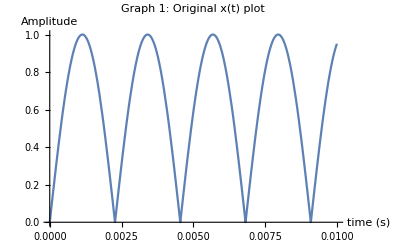

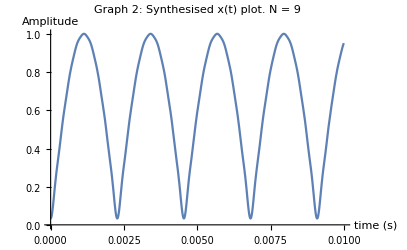
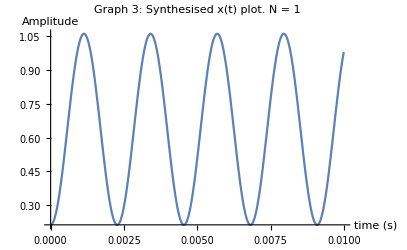

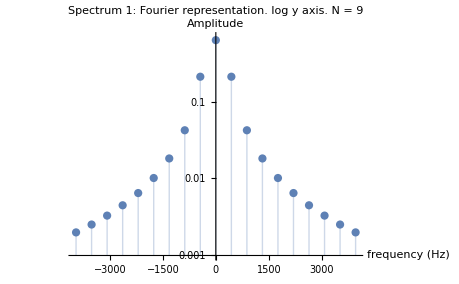
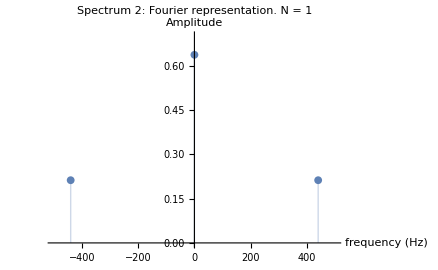

## Explaining the methods

In order to find the Fourier representation of our signal x(t)=|Sin(2π f0 t)| the following Fourier Analysis Integral needs to be solved in order to find the complex amplitude, dependant on the variable k:

ak=1/T0∫_0^T0 Sin[2 π f0 t]ⅇ^(-ⅈ(2π/T0)k t)ⅆt

Where ak is later used for the finite Fourier synthesis summation in order to properly simulate the function x(t). First the period T1 of the function x(t) is found by taking the inverse of its frequency f0. Then the fundamental period T0 can be found by dividing T1 by 2 since the negative curve of the sinusoid is equal to the positive curve caused by the absolute value operator.

In order to execute the synthesis of x(t) the finite Fourier synthesis summation is used:

X[t_]:=∑_(k=-N)^N ak ⅇ^(ⅈ(2π)/T0 k t)

With this, the frequency spectrum of the synthesised signal x(t) can be created.

## Discussing the results

This first graph shows the sinusoidal waves of the original signal x(t)=|Sin(2π f0 t)|. The tops of the wave never dip below zero due to the use of an absolute value operator, which limits the curve to only positive outputs. This will be used as a base to compare the two different synthesised versions, both of which make two different assumptions about the sampling frequency used.

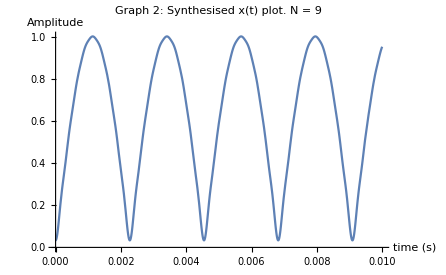
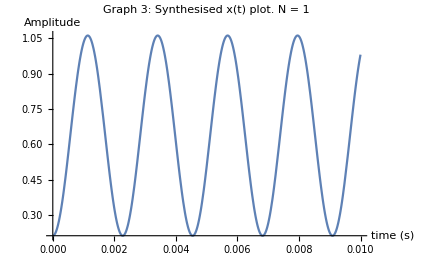

Above in Graph 2 and 3,  the two different synthesised plots of x(t) are shown. Fourier Synthesis uses the complex amplitudes ak, and combines them with the complex exponential shown in the formula:  X(t)=∑_(k=-N)^N ak ⅇ^(ⅈ(2π)/T0 k t). The frequency of the complex exponential is defined as f1=k/T0, where  -N<=k>=N. This means that the value of the max frequency of the Fourier synthesis is tied to the value of N, and as the Nyquist rate defines valid sampling frequencies by the formula: when k = N, f1=fmax <fs/2. Finite Fourier transforms become more accurate to the original function when the N is larger, but here it seems N is given an upper bound. Since  fmax=N/T0 , and fmax <fs/2, that means, N <(fs * T0)/2. For Graph 2, this means that N at largest can have the integer value of 9, and for Graph 3, N can have the largest integer value of 1. Which also explains why the graphs end up looking slightly different to the original signal x(t), due to the sampling of said signal, the maximum value of N used to accurately synthesise is limited, meaning the reconstruction itself becomes limited, caused by the sampling frequency used. A higher sampling frequency would allow for higher values of N, making the reconstruction more accurate.

In Spectrum 1 and Spectrum 2, the complex amplitudes calculated from the Fourier Analysis Integral are put in a frequency spectrum to represent the spectrum of the Fourier representation. In order to best show Spectrum 1, the y-axis was represented logarithmically in order to get a more clear view of the amplitudes in relation to their frequency. Both spectrum’s are limited to their respective Nyquist rates, -fs/2<fmax <fs/2. As can be noted from each spectrum is that the amount of spectral lines at each side of the origin is equal to the size of the N value used. These represent the complex amplitudes and are located at each of the complex exponential frequencies. The bandwidth of each spectrum is represented by their minimum frequency subtracted from their maximum frequency, in this case it comes out to:
Bandwidth spectrum 1: 7920 Hz
Bandwidth spectrum 2: 880 Hz
And defines the frequencies in which the signal itself operates in.

## Code section

Our Code:

```mathematica
f0=220 ; (*Hz*)
```

```mathematica
(*The signal that shall be synthesized*)
```

```mathematica
x[t_]:=Abs[Sin[2 π f0 t]]
```

```mathematica
Ax[t_]:=Sin[2 π f0 t]
```

```mathematica
(*Original plot*)
```

```mathematica
Plot[x[t],{t,0,0.01},AxesLabel->{"time (s)","Amplitude"}, PlotLabel->"Graph 1: Original x(t) plot"]
```

-Graphics-

```mathematica
(********************************* a och b *************************************)
```

```mathematica
T1=1/f0 ;(*period*)
```

```mathematica
T0=T1/2;(*fundemental period*)
```

```mathematica
ak=1/T0∫_0^T0 Ax[t] ⅇ^(-ⅈ(2π/T0)k t)ⅆt (*Fourier Analysis Integral*)
```

(440 (1+ⅇ^(-2 ⅈ k π)))/(440 π-1760 k^2 π)

```mathematica
XN[t_]:=∑_(k=-N1)^N1 ak ⅇ^(ⅈ(2π)/T0 k t) (*limited Fourier Synthesis summation*)
```

```mathematica
(*********************************** c. Find N *********************************)
```

```mathematica
fs1=8000; (*assume sampling rate. Hz*)
```

```mathematica
MaxCos=Cos[2 π *N/T0 t] (*The maximum value cos from N and (-N) in the fourier synthesis.*)
```

Cos[880 N π t]

```mathematica
(*2 fmax < fs. Nyquist rate must be true for no aliasing to occur.*)
(*reduce equation for upper bound limit*)
```

```mathematica
Reduce[2 fMax <fs1]
```

fMax<4000

```mathematica
fmax=3999; (*put fmax under upper bound limit*)
```

```mathematica
(*equtaion for fmax: fmax= N /T0 ;*)
```

```mathematica
N1=Round[fmax T0](*find N from fmax. based on the fmax equation above. Round to closest integer*)
```

9

```mathematica
(*The biggest N value for no aliasing with an fs of 8000 Hz is 9.*)
```

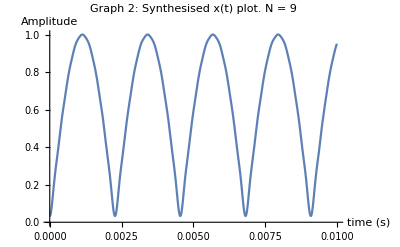

```mathematica
Plot[XN[t],{t,0,0.01},AxesLabel->{"time (s)","Amplitude"}, PlotLabel->"Graph 2: Synthesised x(t) plot. N = 9"]
```

```mathematica
(***************************************** d, Find N *******************************)
```

```mathematica
fs2=1000; (*assume sampling rate. Hz*)
```

```mathematica
MaxCos2=Cos[2 π *N/T0 t] (*The maximum value cos from N and (-N) in the fourier synthesis.*)
```

Cos[880 N π t]

```mathematica
(*2 fmax < fs. Nyquist rate must be true for no aliasing to occur.*)
(*reduce equation for upper bound limit*)
```

```mathematica
Reduce[2 fMax2 <fs2]
```

fMax2<500

```mathematica
fmax2=499; (*put fmax under upper bound limit*)
```

```mathematica
(*equtaion for fmax: fmax=(N /T0 );*)
```

```mathematica
N2=Round[ fmax2 T0](*find N from fmax. based on the fmax equation above. Round to closest integer*)
```

1

```mathematica
(*The biggest N value for no aliasing with an fs of 1000 Hz is 1.*)
```

```mathematica
XN2[t_]:=∑_(k=-N2)^N2 ak ⅇ^(ⅈ(2π)/T0 k t) (*Fourier Synthesis summation*)
```

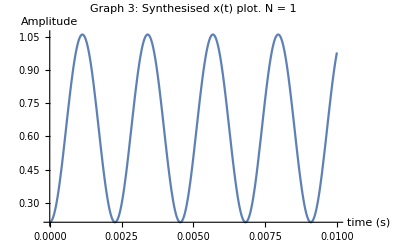

```mathematica
Plot[XN2[t],{t,0,0.01},AxesLabel->{"time (s)","Amplitude"}, PlotLabel->"Graph 3: Synthesised x(t) plot. N = 1"]
```

```mathematica
(*************************** e, plot the spectrums. Find bandwidth ********************************'*)
```

```mathematica
(*discrete spectrum when fs = 8000*)
```

```mathematica
(*The bandwidth is our limit N1 - (-N1)*)
```

```mathematica
bandwidth1=(N1/T0)-(-(N1/T0)) (*Hz*)
```

7920

```mathematica
(*generate coordinates with frequency and amplitude*)
```

```mathematica
B1=Table[{k/T0,Abs[ak]},{k,-N1,N1}];
```

```mathematica
(*Plot the spectrum*)
```

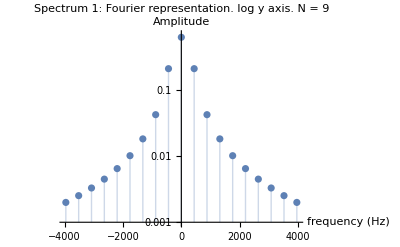

```mathematica
ListPlot[B1,PlotRange->{{-fs1 /2 ,fs1 /2},{0,0.7}},AxesLabel->{"frequency (Hz)","Amplitude"}, PlotLabel->"Spectrum 1: Fourier representation. log y axis. N = 9",Filling->Axis,ScalingFunctions->{None,"Log"}]
```

```mathematica
(*discrete spectrum when fs = 1000*)
```

```mathematica
(* The bandwidth is our limit N1 - (-N1) *)
```

```mathematica
bandwidth2=(N2/T0)-(-(N2/T0))(*Hz*)
```

880

```mathematica
(*generate coordinates with frequency and amplitude*)
```

```mathematica
B2=Table[{k/T0,Abs[ak]},{k,-N2,N2}];
```

```mathematica
(*Plot the spectrum*)
```

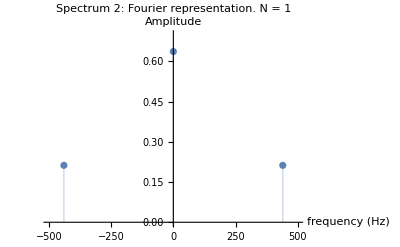

```mathematica
ListPlot[B2,PlotRange->{{-1000/2,1000/2},{0,0.7}},AxesLabel->{"frequency (Hz)","Amplitude"}, PlotLabel->"Spectrum 2: Fourier representation. N = 1",Filling->Axis]
```